## Const:

```mathematica
err0=0.0001;
k1=0.6;
maxMode=5; (*Magnet quantum number m*)
Nsize=40; (*Size of matrix*)
Npoints=500;
C1=1;(*C*)
b=0.6; (*Magnetic field*)
Dz=1; (*Dzyaloshiskiy-Morya interaction const*)
An=0.0; (*Anisotropy const*)
(*R0 = 3.7;*)
(*a0=0.96*Sqrt[π/2]R0/3^(1/4)*)(*size of lattice const*)
ϕ0=0; (* 0, π/3, 2π/3, ..., 5π/3 which circle (not important)*)
m=1;
fromR0=3;
toR0=6;
tableEnergy={};
densEnergy=Table[
Setka=Table[N[R0/Npoints k],{k,1,Npoints}];
Setka=Prepend[Setka,err0];
beta=β/.NDSolve[{(Sin[β[r]] (2An Cos[β[r]] r^2+b r^2+ C1 Cos[β[r]]-2 Dz r Sin[β[r]]))/r==C1 β'[r]+C1 r β''[r],β[err0]==π-√(b)err0,β[R0]==err0},β,{r,10^-5,R0},Method->{"Shooting", "StartingInitialConditions"->{β[err0]==π-√(b)k1 err0 , β'[err0] == -√(b) k1}} ]⟦1⟧;
wdens[r_]:=r (b(1-Cos[beta[r]])+An(1-(Cos[beta[r]])^2)+(Dz Cos[beta[r]] Sin[beta[r]])/r+(C1 Sin[beta[r]]^2)/(2 r^2)+Dz beta'[r]+1/2 C1 beta'[r]^2);
wdensTable=wdens[Setka];
W=2/(3 Npoints) Sum[ wdensTable⟦k-1⟧+4wdensTable⟦k⟧+wdensTable⟦k+1⟧,{k,2,Npoints,2}]/ R0;
{R0,W},{R0,fromR0,toR0,0.05}];
Ropt=MinimalBy[densEnergy,Last][[1,1]];
BZ=Table[N[BesselJZero[m,k],7],{m,0,maxMode},{k,1,Nsize}];
a0=Sqrt[π/2]Ropt/3^(1/4);
R0=a0/Cos[π/6]
```

4.39854

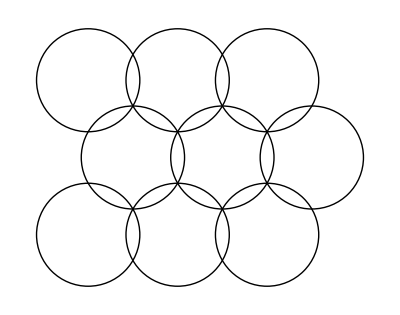

```mathematica
Graphics[Table[Circle[{i+((-1)^j+1)/4,Sqrt[3]/2j}, R0/(2a0)  (*3^(1/4)/(√(2 π))*) ],{i,3},{j,3}]]
```

## Dispersion:

```mathematica
Setka=Table[err0 KroneckerDelta[0,k]+R0/Npoints k,{k,0,Npoints}];

λn[n_,m_]:=(BZ[[Abs[m]+1]][[n]]/R0)^2;
ϕn[n_,r_,m_]:=Sqrt[2]/Abs[R0 ((D[BesselJ[m,rr1],rr1])/.rr1->BZ[[Abs[m]+1]][[n]])] BesselJ[m,BZ[[Abs[m]+1]][[n]]/R0 r];

pnt[x0_]:=
Module[{k=1},
min1=Abs[x0-Setka⟦k⟧];
Do[If[Abs[x0-Setka⟦k1⟧]<Abs[x0-Setka⟦k⟧],k=k1;],{k1,1,Npoints+1}];
k
];
hϕ=ArcCos[a0/R0]/50;
ϕ1[r_,ϕ_]:=ArcSin[r Sin[ϕ-ϕ0]/Sqrt[r^2+4 a0^2-4 a0 r Cos[ϕ-ϕ0]]]+Pi+ϕ0;
r1[r_,ϕ_]:=Sqrt[r^2+4 a0^2-4a0 r Cos[ϕ-ϕ0]];
ϕtable =Table[ϕ,{ϕ,ϕ0-ArcCos[a0/R0] ,ϕ0+ArcCos[a0/R0],hϕ}];
pntTable=Table[{ϕ,Table[pnt[r1[Setka⟦k⟧,ϕ]],{k,1,Npoints+1}]},{ϕ,ϕ0-ArcCos[a0/R0] ,ϕ0+ArcCos[a0/R0],hϕ}];

exchRadialF1[k1_,k2_,kt_]:=R0/(3 (Npoints))Sum[
ⅇ^(ⅈ (m) ϕ1[Setka⟦k-1⟧,ϕtable⟦kt⟧]) matrxϕn1⟦k1,k-1⟧matrxϕn1⟦k2,pntTable⟦kt⟧⟦2⟧⟦k-1⟧⟧(C1 λn1[k1]Setka⟦k-1⟧+pointsFuncV0⟦k-1⟧+m pointsFuncV1⟦k-1⟧)+

4 ⅇ^(ⅈ  (m) ϕ1[Setka⟦k⟧,ϕtable⟦kt⟧])matrxϕn1⟦k1,k⟧matrxϕn1⟦k2,pntTable⟦kt⟧⟦2⟧⟦k⟧⟧(C1 λn1[k1]Setka⟦k⟧+pointsFuncV0⟦k⟧+m pointsFuncV1⟦k⟧)+

ⅇ^(ⅈ (m) ϕ1[Setka⟦k+1⟧,ϕtable⟦kt⟧])matrxϕn1⟦k1,k+1⟧matrxϕn1⟦k2,pntTable⟦kt⟧⟦2⟧⟦k+1⟧⟧(C1 λn1[k1]Setka⟦k+1⟧+pointsFuncV0⟦k+1⟧+m pointsFuncV1⟦k+1⟧),

{k,pnt[-√(-2 a0^2+R0^2+2 a0^2 Cos[2 ϕtable⟦kt⟧-2 ϕ0])+2 a0 Cos[ϕtable⟦kt⟧-ϕ0]],Npoints,2}];

exchRadialF2[k1_,k2_,kt_]:=
R0/(3 (Npoints))Sum[
ⅇ^(ⅈ  (m) ϕ1[Setka⟦k-1⟧,ϕtable⟦kt⟧]) matrxϕn2⟦k1,k-1⟧matrxϕn2⟦k2,pntTable⟦kt⟧⟦2⟧⟦k-1⟧⟧(C1 λn2[k1]Setka⟦k-1⟧+pointsFuncV0⟦k-1⟧-m pointsFuncV1⟦k-1⟧)+

4 ⅇ^(ⅈ  (m) ϕ1[Setka⟦k⟧,ϕtable⟦kt⟧])matrxϕn2⟦k1,k⟧matrxϕn2⟦k2,pntTable⟦kt⟧⟦2⟧⟦k⟧⟧(C1 λn2[k1]Setka⟦k⟧+pointsFuncV0⟦k⟧-m pointsFuncV1⟦k⟧)+

ⅇ^(ⅈ  (m) ϕ1[Setka⟦k+1⟧,ϕtable⟦kt⟧])matrxϕn2⟦k1,k+1⟧matrxϕn2⟦k2,pntTable⟦kt⟧⟦2⟧⟦k+1⟧⟧(C1 λn2[k1]Setka⟦k+1⟧+pointsFuncV0⟦k+1⟧-m pointsFuncV1⟦k+1⟧),

{k,pnt[-√(-2 a0^2+R0^2+2 a0^2 Cos[2 ϕtable⟦kt⟧-2 ϕ0])+2 a0 Cos[ϕtable⟦kt⟧-ϕ0]],Npoints,2}];

exchRadialG[k1_,k2_,kt_]:=R0/(3 Npoints)Sum[
ⅇ^(ⅈ (m) ϕ1[Setka⟦k-1⟧,ϕtable⟦kt⟧]) matrxϕn1⟦k1,k-1⟧matrxϕn2⟦k2,pntTable⟦kt⟧⟦2⟧⟦k-1⟧⟧pointsFuncG⟦k-1⟧+
4 ⅇ^(ⅈ  (m) ϕ1[Setka⟦k⟧,ϕtable⟦kt⟧])matrxϕn1⟦k1,k⟧matrxϕn2⟦k2,pntTable⟦kt⟧⟦2⟧⟦k⟧⟧pointsFuncG⟦k⟧+
ⅇ^(ⅈ  (m)ϕ1[Setka⟦k+1⟧,ϕtable⟦kt⟧])matrxϕn1⟦k1,k+1⟧matrxϕn2⟦k2,pntTable⟦kt⟧⟦2⟧⟦k+1⟧⟧pointsFuncG⟦k+1⟧,{k,pnt[-√(-2 a0^2+R0^2+2 a0^2 Cos[2 ϕtable⟦kt⟧-2 ϕ0])+2 a0 Cos[ϕtable⟦kt⟧-ϕ0]],Npoints,2}];


exchF1[k1_,k2_]:=
Chop[hϕ Sum[ⅇ^(-ⅈ  (m) ϕtable⟦j⟧)exchRadialF1[k1,k2,j],{j,1,Length[ϕtable] }]];

exchF2[k1_,k2_]:=
 Chop[hϕ Sum[ⅇ^(-ⅈ  (m) ϕtable⟦j⟧)exchRadialF2[k1,k2,j],{j,1,Length[ϕtable] }]];

exchG[k1_,k2_]:=
Chop[hϕ Sum[ⅇ^(-ⅈ  (m) ϕtable⟦j⟧) exchRadialG[k1,k2,j],{j,1,Length[ϕtable] }]];

thetaFunc[x_,y_]:=If[(x^2+y^2≤R0^2)&&((x-2 a0)^2+y^2≤R0^2),1,0];

exchF1Exact[k1_,k2_]:=NIntegrate[
ⅇ^(-ⅈ  (m) ArcTan[y/x])ⅇ^(ⅈ  (m)(Pi-ArcTan[y/(2 a0-x)]))
 ϕn1[k1,√(x^2+y^2)] ϕn1[k2,√((x-2 a0)^2+y^2)]( C1 λn1[k1]+(funcV0[√(x^2+y^2)]+m funcV1[√(x^2+y^2)])/√(x^2+y^2)) thetaFunc[x,y],{x,-R0,R0},{y,-R0,R0}];

exchF2Exact[k1_,k2_]:=NIntegrate[ⅇ^(-ⅈ  (m)ArcTan[y/x])ⅇ^(ⅈ  (m) (Pi-ArcTan[y/(2 a0-x)]))  ϕn2[k1,√(x^2+y^2)] ϕn2[k2,√((x-2 a0)^2+y^2)]( C1 λn2[k1]+(funcV0[√(x^2+y^2)]-m funcV1[√(x^2+y^2)])/√(x^2+y^2)) thetaFunc[x,y],{x,-R0,R0},{y,-R0,R0}];

exchGExact[k1_,k2_]:=NIntegrate[ⅇ^(-ⅈ  (m) ArcTan[y/x])ⅇ^(ⅈ (m) (Pi-ArcTan[y/(2 a0-x)]))ϕn1[k1,√(x^2+y^2)]ϕn2[k2,√((x-2 a0)^2+y^2)]  (funcG[√(x^2+y^2)]/√(x^2+y^2)) thetaFunc[x,y],{x,-R0,R0},{y,-R0,R0}];
```

```mathematica
tableMatricies={}
```

{}

```mathematica
Print["R_0 is ", R0];
Print["a_0 is ", a0];
Do[

λn1[n_]         :=λn[n,       m+1];
ϕn1[n_,r_]:=ϕn[n,r,m+1];

λn2[n_]         :=λn[n,       m-1];
ϕn2[n_,r_]:=ϕn[n,r,m-1];


matrxϕn1=Parallelize[Table[ϕn1[k,Setka],{k,1,Nsize}]];
matrxϕn2=Parallelize[Table[ϕn2[k,Setka],{k,1,Nsize}]];

beta=β/.NDSolve[{(Sin[β[r]] (2An Cos[β[r]] r^2+b r^2+C1 Cos[β[r]]-2 Dz r Sin[β[r]]))/r==C1 β'[r]+r C1 β''[r],β[err0]==π-√(b)err0,β[R0]==err0},β,{r,10^-5,R0},Method->{"Shooting", "StartingInitialConditions"->{β[err0]==π-√(b)k1 err0 , β'[err0] == -√(b)k1 }} ]⟦1⟧;

βmin[r_]:=beta[r];
dβmin[r_]:=beta'[r];
funcV0[r_]:=r(1/2 An(1+3Cos[2βmin[r]])+ b Cos[βmin[r]]+(3 C1 (Cos[2 βmin[r]]-1))/(4 r^2)-(3 Dz Cos[βmin[r]] Sin[βmin[r]])/r-Dz dβmin[r]-1/2 C1( dβmin[r])^2);
funcV1[r_]:=r(-(2 C1 (Cos[βmin[r]]+1))/r^2+(2 Dz Sin[βmin[r]])/r);
funcG[r_]:=r(1/2 An  (Sin[βmin[r]])^2+(C1 Sin[βmin[r]]^2)/(2 r^2)+(Dz Sin[2βmin[r]])/(2 r)-Dz dβmin[r]-1/2 C1 (dβmin[r])^2);



pointsFuncV0=funcV0[Setka];
pointsFuncV1=funcV1[Setka];
pointsFuncG=funcG[Setka];

(*It's Simpson's rule*)

 F1[k1_,k2_]:=KroneckerDelta [k1 ,k2 ]C1 (λn1[k1])+R0/(3 Npoints) Sum[ matrxϕn1⟦k1,k-1⟧
matrxϕn1⟦k2,k-1⟧(pointsFuncV0⟦k-1⟧+m pointsFuncV1⟦k-1⟧)+
4matrxϕn1⟦k1,k⟧matrxϕn1⟦k2,k⟧(pointsFuncV0⟦k⟧+m pointsFuncV1⟦k⟧)+
matrxϕn1⟦k1,k+1⟧matrxϕn1⟦k2,k+1⟧(pointsFuncV0⟦k+1⟧+m pointsFuncV1⟦k+1⟧),{k,2,Npoints,2}];

 F2[k1_,k2_]:=KroneckerDelta [k1 ,k2 ]C1 (λn2[k1])+R0/(3 Npoints) Sum[ matrxϕn2⟦k1,k-1⟧
matrxϕn2⟦k2,k-1⟧(pointsFuncV0⟦k-1⟧-m pointsFuncV1⟦k-1⟧)+4matrxϕn2⟦k1,k⟧
matrxϕn2⟦k2,k⟧(pointsFuncV0⟦k⟧-m pointsFuncV1⟦k⟧)+matrxϕn2⟦k1,k+1⟧
matrxϕn2⟦k2,k+1⟧(pointsFuncV0⟦k+1⟧-m pointsFuncV1⟦k+1⟧),{k,2,Npoints,2}];

 G[k1_,k2_]:=R0/(3 Npoints) Sum[ 
matrxϕn1⟦k1,k-1⟧matrxϕn2⟦k2,k-1⟧pointsFuncG⟦k-1⟧+
4matrxϕn1⟦k1,k⟧matrxϕn2⟦k2,k⟧pointsFuncG⟦k⟧+
matrxϕn1⟦k1,k+1⟧matrxϕn2⟦k2,k+1⟧pointsFuncG⟦k+1⟧,{k,2,Npoints,2}];

     F1table=Table[If[i<=j,F1[i,j],0],{i,1,Nsize},{j,1,Nsize}];
For[i=1,i≤Nsize,i++,
(For[k=1,k≤Nsize,k++,F1table⟦k,i⟧=F1table⟦i,k⟧])
];

     F2table=Table[If[i<=j,F2[i,j],0],{i,1,Nsize},{j,1,Nsize}];
For[i=1,i≤Nsize,i++,
(For[k=1,k≤Nsize,k++,F2table⟦k,i⟧=F2table⟦i,k⟧])
];

 Gtable=Table[G[i,j],{i,1,Nsize},{j,1,Nsize}];

matrixHdG=ArrayFlatten[{{F1table, Gtable}, {-Transpose[Gtable], -F2table}}];

moda0=Chop[Eigenvalues[matrixHdG]];

Do[If[Im[moda0⟦i⟧]>err0,Print[Style["There is a complex value! R_0=",18,Red],R0,", E[",i,"]=",moda0⟦i⟧] ],{i,1,2 Nsize}];

If[Length[Select[moda0,#>0&]]==Length[Select[moda0,#<0&]],Print["Number of positive values equals to number of negative ones"],Print[Style["Alarm!!! Number of positive values NOT equals to number of negative ones",18,Red]]];

mPositive=Sort[Select[moda0,#>0&],Abs[#1]<Abs[#2]&];
mNegative=Sort[Select[moda0,#<0&],Abs[#1]<Abs[#2]&];

Print["m is ", m];
Print["Energy for modes "];
Print[Table[mPositive⟦k⟧,{k,1,8}],  " m = ", m];
Print[Table[Abs[mNegative⟦k⟧],{k,1,8}], " m = ", -m];


{eigvlH,eigvecH}=Eigensystem[matrixHdG];

exchF1t=Parallelize[Table[exchF1[i,j],{i,1,Nsize},{j,1,Nsize}]];
  exchF2t=Parallelize[Table[exchF2[i,j],{i,1,Nsize},{j,1,Nsize}]];
  exchGt=Parallelize[Table[exchG[i,j],{i,1,Nsize},{j,1,Nsize}]];

matrixExch=ArrayFlatten[{{exchF1t, exchGt}, {-Transpose[exchGt], -exchF2t}}];

vecZeroMode1=eigvecH[[2Nsize]];
E01=vecZeroMode1.matrixHdG.vecZeroMode1;
Et1=vecZeroMode1.matrixExch.vecZeroMode1;
Print["m=",-m," E0=",E01," Et=",Et1];

vecZeroMode2=eigvecH[[2Nsize-1]];
E02=vecZeroMode2.matrixHdG.vecZeroMode2;
Et2=vecZeroMode2.matrixExch.vecZeroMode2;
Print["m=",m," E0=",E02," Et=",Et2];
AppendTo[tableMatricies,{m,matrixHdG,matrixExch}];
AppendTo[tableEnergy,{-m,E01,Et1}];
AppendTo[tableEnergy,{m,E02,Et2}];

,{m,0,4}]
```

R_0 is 4.39854

a_0 is 3.80925

Number of positive values equals to number of negative ones

m is 0

Energy for modes

{0.840798,3.04134,5.89711,9.73747,14.5909,20.4615,27.3507,35.2594} m = 0

{0.840798,3.04134,5.89711,9.73747,14.5909,20.4615,27.3507,35.2594} m = 0

$Aborted

## Plot:

```mathematica
m1=tableMatricies[[2,1]]
matrixHdG=tableMatricies[[2,2]];
matrixExch=tableMatricies[[2,3]];
{eigvlH,eigvecH}=Eigensystem[matrixHdG];
vecZeroMode=eigvecH[[2Nsize-2]];
E0m1n2=vecZeroMode.matrixHdG.vecZeroMode;
Etm1n2=vecZeroMode.matrixExch.vecZeroMode;
Print["m=",-m1," E0m1n2 =",E0m1n2," Etm1n =",Etm1n2];

m2=tableMatricies[[3,1]]
matrixHdG=tableMatricies[[3,2]];
matrixExch=tableMatricies[[3,3]];
{eigvlH,eigvecH}=Eigensystem[matrixHdG];
vecZeroMode=eigvecH[[2Nsize-2]];
E0m2n2=vecZeroMode.matrixHdG.vecZeroMode;
Etm2n2=vecZeroMode.matrixExch.vecZeroMode;
Print["m=",-m2," E0m2n2 =",E0m2n2," Etm2n =",Etm2n2];

m3=tableMatricies[[4,1]]
matrixHdG=tableMatricies[[4,2]];
matrixExch=tableMatricies[[4,3]];
{eigvlH,eigvecH}=Eigensystem[matrixHdG];
vecZeroMode=eigvecH[[2Nsize-2]];
E0m3n2=vecZeroMode.matrixHdG.vecZeroMode;
Etm3n2=vecZeroMode.matrixExch.vecZeroMode;
Print["m=",-m3," E0m3n2 =",E0m3n2," Etm3n =",Etm3n2];
```

1

m=-1 E0m1n2 =-1.76603 Etm1n =0.181073

2

m=-2 E0m2n2 =-2.40474 Etm2n =-0.384781

3

m=-3 E0m3n2 =-3.26774 Etm3n =0.66563

```mathematica
tableEnergy
```

{{0,0.7937,0.0452689},{0,-0.7937,-0.0452689},{-1,-0.0517958,0.0054382},{1,1.53087,-0.123226},{-2,-0.317037,-0.0608424},{2,2.27275,0.257397},{-3,-1.0317,0.189729},{3,3.03221,-0.451175},{-4,-2.02934,-0.377282},{4,3.85437,0.717407}}

```mathematica
mode0[kx_,ky_]:=  Abs[(tableEnergy⟦2⟧⟦2⟧+2/(2π)( Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2])tableEnergy⟦2⟧⟦3⟧)];

modeM1n2[kx_,ky_]:=Abs[(E0m1n2+2/(2π)( Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2])Etm1n2)];
modeM2n2[kx_,ky_]:=Abs[(E0m2n2+2/(2π)( Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2])Etm2n2)];
modeM3n2[kx_,ky_]:=Abs[(E0m3n2+2/(2π)( Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2])Etm3n2)];

modeM1[kx_,ky_]:=Abs[(tableEnergy⟦3⟧⟦2⟧+2/(2π)( Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2])tableEnergy⟦3⟧⟦3⟧)];
mode1[kx_,ky_]:=  Abs[(tableEnergy⟦4⟧⟦2⟧+2/(2π)( Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2])tableEnergy⟦4⟧⟦3⟧)];
modeM2[kx_,ky_]:=Abs[(tableEnergy⟦5⟧⟦2⟧+2/(2π)( Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2])tableEnergy⟦5⟧⟦3⟧)];
mode2[kx_,ky_]:=  Abs[(tableEnergy⟦6⟧⟦2⟧+2/(2π)( Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2])tableEnergy⟦6⟧⟦3⟧)];
modeM3[kx_,ky_]:=Abs[(tableEnergy⟦7⟧⟦2⟧+2/(2π)( Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2])tableEnergy⟦7⟧⟦3⟧)];
mode3[kx_,ky_]:=  Abs[(tableEnergy⟦8⟧⟦2⟧+2/(2π)( Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2])tableEnergy⟦8⟧⟦3⟧)]
modeM4[kx_,ky_]:=Abs[(tableEnergy⟦9⟧⟦2⟧+2/(2π)( Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2])tableEnergy⟦9⟧⟦3⟧)];
```

```mathematica
RRR=2π;
Hexagone=Interpolation[Table[{a,RRR {Cos[a],Sin[a]}},{a,-π,π,π/3}],InterpolationOrder->1];
Plot3D[{modeM1[x,y],modeM1n2[x,y],modeM2[x,y],mode0[x,y],mode1[x,y](*,modeM2n2[x,y],modeM3[x,y],modeM3n2[x,y]*)},{x,-RRR,RRR},{y,-RRR,RRR},Mesh -> 20,PlotStyle->Table[Hue[k*0.7],{k,1,6}],PlotLegends->{"m = -1, n = 1","m = -1, n = 2","m = -2, n = 1","m = 0, n = 1","m = 1, n = 1","m = -2, n = 2","m = -3, n = 1","m = -3, n = 2"},RegionFunction->Function[{x,y,z},Norm@{x,y}≤Norm@Hexagone[ArcTan[y,x+0.00001]]]
,PlotRange->{{-2π,2π},{-2π,2π},{0,2}}]
```

-Graphics3D-

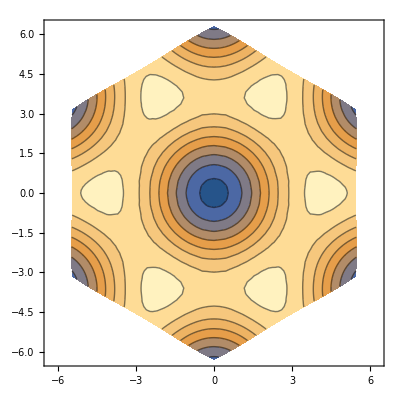

0.0466027

```mathematica
ContourPlot[{modeM1[x,y]},{x,-RRR,RRR},{y,-RRR,RRR},RegionFunction->Function[{x,y,z},Norm@{x,y}≤Norm@Hexagone[ArcTan[y,x+0.00001]]]]
modeM1[0,0]
```

```mathematica
Plot3D[{modeM1[x,y]},{x,-RRR,RRR},{y,-RRR,RRR},RegionFunction->Function[{x,y,z},Norm@{x,y}≤Norm@Hexagone[ArcTan[y,x+0.00001]]],ColorFunction->Function[{x,y,z},Hue[.65 (1-z)]]]
modeM1[0,0]
```

-Graphics3D-

0.0466027